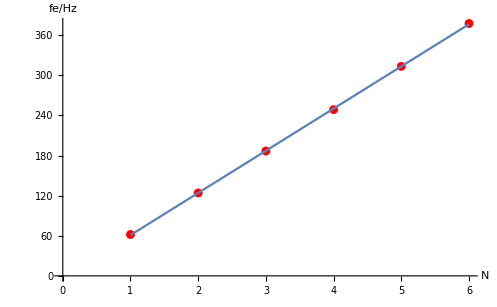
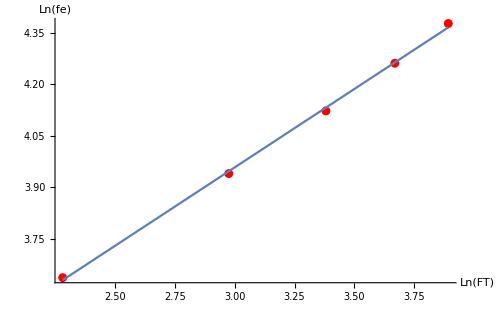
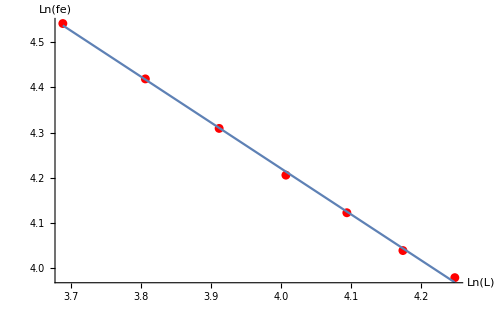
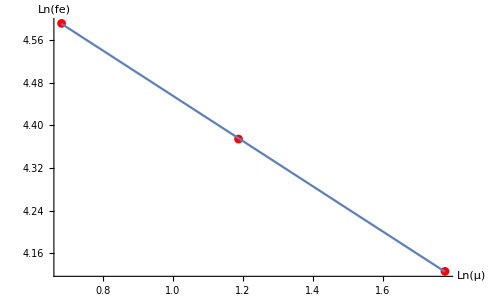
实验报告
系别：物理  班号：9组9号  姓名：盛凯枫  学号：1500011404  实验日期：2017年4月14日
实验名称：弦上驻波实验

一、实验数据和现象
1. 弦线线密度的测量数据
弦线直径d0=1.067mm，长度l=397.3mm，质量m=2.35g，线密度μ=5.91g/m

2. 对同一弦线、固定有效长度和张力，共振频率与驻波波腹个数的关系，记录弦线从起振到共振的实验现象
FT=3Mg,M=1000.1g,L=60.0cm,vc=70.5m/s
*说明：fe实际可以读出2位小数，但仅精确到一位小数是因为在判断共振时，振幅在一段范围内均几乎不变，且振幅在不断波动，波动幅度大于振幅改变量，故实际有意义的数字仅有一位小数（下同）
N | 1 | 2 | 3 | 4 | 5 | 6
fc/Hz | 58.8 | 117.5 | 176.3 | 235. | 293.8 | 352.5
fe/Hz | 61.9 | 124.1 | 186.8 | 248.8 | 313.5 | 377.7
|(fe-fc)/fc|/% | 5.4 | 5.6 | 6. | 5.9 | 6.7 | 7.2
ve/m/s | 74.3 | 74.4 | 74.7 | 74.6 | 75.2 | 75.5
弦线从起振到共振的实验现象:当频率逐渐增大至共振频率附近时，探测器信号振幅显著增大，且存在像行波一样的波形运动；当频率逐渐增大，波形变得稳定，振幅也迅速增大，当振幅增大到某一程度后，再增大频率则会导致振幅突然迅速降低

3. 对同一弦线、固定有效长度，共振频率（基频）与弦线张力的关系
有效长度L=60.0cm,N=1
FT/N | 9.801 | 19.602 | 29.403 | 39.204 | 49.005
fc/Hz | 33.9 | 48. | 58.8 | 67.8 | 75.8
fe/Hz | 38. | 51.4 | 61.7 | 70.9 | 79.6
|(fe-fc)/fc|/% | 12. | 7.2 | 5. | 4.5 | 4.9
Ln(fe) | 3.64 | 3.94 | 4.12 | 4.26 | 4.38
Ln(FT) | 2.28 | 2.98 | 3.38 | 3.67 | 3.89
4. 对同一弦线、固定张力，共振频率（基频）与弦线有效长度的关系
张力FT=3Mg,N=1
L/cm | 40. | 45. | 50. | 55. | 60. | 65. | 70.
fc/Hz | 88.1 | 78.3 | 70.5 | 64.1 | 58.8 | 54.2 | 50.4
fe/Hz | 93.8 | 83. | 74.4 | 67.1 | 61.8 | 56.8 | 53.5
|(fe-fc)/fc|/% | 6.4 | 6. | 5.5 | 4.7 | 5.1 | 4.7 | 6.2
Ln(fe) | 4.48 | 4.36 | 4.26 | 4.16 | 4.07 | 3.99 | 3.92
Ln(L) | 3.69 | 3.81 | 3.91 | 4.01 | 4.10 | 4.17 | 4.25
5. 更换弦线、固定有效长度和张力，共振频率（基频）与弦线线密度的关系
N=1,L=60.0cm,FT=3Mg
μ/g/m | 5.91 | 3.28 | 1.98
fc/Hz | 58.8 | 78.9 | 101.5
fe/Hz | 61.9 | 79.4 | 98.7
|(fe-fc)/fc|/% | 5.4 | 0.63 | 2.8
Ln(fe) | 4.07 | 4.37 | 4.62
Ln(μ) | 1.78 | 1.19 | 0.683

二、实验数据和现象的分析、处理和结论
1. 分析总结如何确定判断弦线共振的判据
判断依据：逐渐增大频率，当探测器信号振幅达到最大且能够长时间保持时，即再增大频率就会导致振幅大幅减小时，即可判断弦线达到了共振

2. 利用共振频率与驻波波腹个数的关系数据，测定弦线上横波的传播速度
横坐标为N，纵坐标为fe做线性拟合，得到斜率K=v/2L，则v=2L*K
-Graphics-
拟合直线函数y=-2.14+63.1 x,K=63.1Hz,v=75.7m/s

3. 作图并用最小二乘法作直线拟合，研究共振频率与弦线张力及有效长度的指数关系
共振频率与弦线张力的指数关系
-Graphics-
拟合直线函数y=2.58+0.458x
即fe正比于FT^0.458

共振频率与有效长度的指数关系
-Graphics-
拟合直线函数y=8.28-1.01 x
即fe正比于L^-1.01

4. 用作图法研究共振频率与弦线线密度的指数关系
-Graphics-
拟合直线函数y=4.88-0.427 x
即fe正比于μ^-0.427

三、分析与讨论
分析实验结果，发现对于fe与L关系的测量较为准确，而fe与FT关系测量的误差较大，分析原因在于FT的值准确度较低，杠杆自身重力、杠杆摩擦等均未计入，同时也存在实验方法的问题，在实验初期尚未定出一个较为客观的共振频率判断方案；此外fe与μ间的关系测量误差更大，原因可能是此实验是在不同的仪器上完成的，测量中由于探测器、驱动器等性能的差异以及弦线除了线密度以外的其它差别，都会给实验结果引入误差。

```mathematica
data1=SetAccuracy[{{58.75,117.50,176.25,235.01,293.76,352.51},{61.90,124.06,186.80,248.80,313.50,377.70}},2];
data2=SetAccuracy[{{33.92,47.97,58.75,67.84,75.85},{37.95,51.40,61.70,70.90,79.60}},2];
data3=SetAccuracy[{{40.0,45.0,50.0,55.0,60.0,65.0,70.0},{88.13,78.33,70.50,64.09,58.75,54.23,50.36},{93.80,83.00,74.40,67.10,61.75,56.80,53.50}},2];
data4={{5.91,3.28,1.98},{58.75,78.9,101.5},{61.90,79.4,98.7}}
```

{{5.91,3.28,1.98},{58.75,78.9,101.5},{61.9,79.4,98.7}}

```mathematica
list={Range[6]//Prepend["N"],data1[[1]]//Prepend["fc/Hz"],data1[[2]]//Prepend["fe/Hz"],Abs[data1[[1]]-data1[[2]]]/data1[[1]]*100//Prepend["|(fe-fc)/fc|/%"],2*0.6*data1[[2]]/Range[6]//Prepend["ve/m/s"]}
```

{{N,1,2,3,4,5,6},{fc/Hz,58.8,117.5,176.3,235.,293.8,352.5},{fe/Hz,61.9,124.1,186.8,248.8,313.5,377.7},{|(fe-fc)/fc|/%,5.4,5.6,6.,5.9,6.7,7.15},{ve/m/s,74.28,74.436,74.72,74.64,75.24,75.54}}

```mathematica
{{"N",1,2,3,4,5,6},{"fc/Hz",58.75,117.5,176.25,235.01,293.76,352.51},{"fe/Hz",61.9,124.06,186.8,248.8,313.5,377.7},{"|(fe-fc)/fc|/%",5.361702127659572,5.582978723404257,5.985815602836887,5.8678354112591045,6.7197712418300695,7.145896570310062},{"ve/m/s",74.28,74.43599999999999,74.72,74.64,75.24,75.53999999999999}}
```

{{N,1,2,3,4,5,6},{fc/Hz,58.75,117.5,176.25,235.01,293.76,352.51},{fe/Hz,61.9,124.06,186.8,248.8,313.5,377.7},{|(fe-fc)/fc|/%,5.3617,5.58298,5.98582,5.86784,6.71977,7.1459},{ve/m/s,74.28,74.436,74.72,74.64,75.24,75.54}}

```mathematica
TextGrid[list,Frame->All,ItemSize->Full,Alignment->{Center,Center}]
```

N | 1 | 2 | 3 | 4 | 5 | 6
fc/Hz | 58.8 | 117.5 | 176.3 | 235. | 293.8 | 352.5
fe/Hz | 61.9 | 124.1 | 186.8 | 248.8 | 313.5 | 377.7
|(fe-fc)/fc|/% | 5.4 | 5.6 | 6. | 5.9 | 6.7 | 7.15
ve/m/s | 74.28 | 74.436 | 74.72 | 74.64 | 75.24 | 75.54

```mathematica
list2={9.801*Range[5]//Prepend["FT/N"],data2[[1]]//Prepend["fc/Hz"],data2[[2]]//Prepend["fe/Hz"],Abs[data2[[1]]-data2[[2]]]/data2[[1]]*100//Prepend["|(fe-fc)/fc|/%"],Log[data2[[2]]]//Prepend["Ln(fe)"],Log[9.801*Range[5]]//Prepend["Ln(FT)"]}
```

{{FT/N,9.801,19.602,29.403,39.204,49.005},{fc/Hz,33.9,48.,58.8,67.8,75.8},{fe/Hz,38.,51.4,61.7,70.9,79.6},{|(fe-fc)/fc|/%,12.,7.2,5.,4.5,4.9},{Ln(fe),3.636,3.94,4.122,4.261,4.377},{Ln(FT),2.28248,2.97563,3.3811,3.66878,3.89192}}

```mathematica
TextGrid[list2,Frame->All,ItemSize->Full,Alignment->{Center,Center}]
```

FT/N | 9.801 | 19.602 | 29.403 | 39.204 | 49.005
fc/Hz | 33.9 | 48. | 58.8 | 67.8 | 75.8
fe/Hz | 38. | 51.4 | 61.7 | 70.9 | 79.6
|(fe-fc)/fc|/% | 12. | 7.2 | 5. | 4.5 | 4.9
Ln(fe) | 3.636 | 3.94 | 4.122 | 4.261 | 4.377
Ln(FT) | 2.28248 | 2.97563 | 3.3811 | 3.66878 | 3.89192

```mathematica
l={{3.636269503841639,3.9396381724611196,4.122283930911342,4.2612704335380815,4.377014092850337},{2.2824844212870428,2.975631601846988,3.3810967099551523,3.6687787824069336,3.8919223337211433}}
```

{{3.63627,3.93964,4.12228,4.26127,4.37701},{2.28248,2.97563,3.3811,3.66878,3.89192}}

```mathematica
LinearModelFit[Table[{l[[1,i]],l[[2,i]]},{i,1,5}],x,x]
```

FittedModel[-5.63918+2.18306 x]

```mathematica
%40["AdjustedRSquared"]
```

0.998732

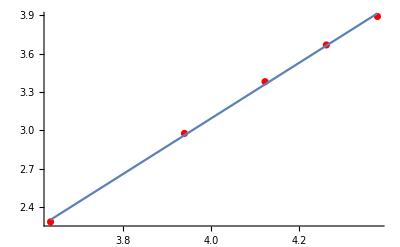

```mathematica
Show[ListPlot[Table[{l⟦1,i⟧,l⟦2,i⟧},{i,1,5}],PlotStyle->Red],Plot[%40[x],{x,3.636269503841639,4.377014092850337}]]
```

```mathematica
list3={data3[[1]]//Prepend["L/cm"],data3[[2]]//Prepend["fc/Hz"],data3[[3]]//Prepend["fe/Hz"],Abs[data3[[2]]-data3[[3]]]/data3[[2]]*100//Prepend["|(fe-fc)/fc|/%"],Log[data3[[2]]]//Prepend["Ln(fe)"],Log[data3[[1]]]//Prepend["Ln(L)"]}
```

{{L/cm,40.,45.,50.,55.,60.,65.,70.},{fc/Hz,88.1,78.3,70.5,64.1,58.8,54.2,50.4},{fe/Hz,93.8,83.,74.4,67.1,61.8,56.8,53.5},{|(fe-fc)/fc|/%,6.4,6.,5.5,4.7,5.1,4.7,6.2},{Ln(fe),4.479,4.361,4.256,4.16,4.073,3.993,3.919},{Ln(L),3.689,3.807,3.912,4.007,4.094,4.174,4.248}}

```mathematica
linearmodelfitlist[l1]
```

FittedModel[8.28-1.015 x]

```mathematica
FittedModel[8.16760048421095800255460535373611300444`4.168954454831124-0.99998964754340882426833642190625497728`4.168954454831124 x][x]
```

8.168-1. x

```mathematica
Show[Plot[FittedModel[8.16760048421095800255460535373611300444`4.168954454831124-0.99998964754340882426833642190625497728`4.168954454831124 x][x],{x,list[[1,1]],list[[1,Length[list[[1]]]]]}]]
```

```mathematica
l1={}
```

{{3.689,3.807,3.912,4.007,4.094,4.174,4.248},{4.541,4.419,4.309,4.206,4.123,4.04,3.98}}

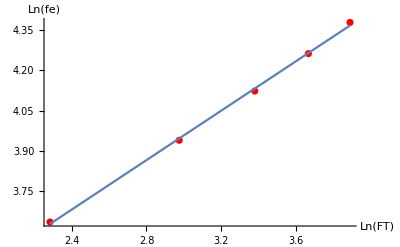

```mathematica
plotlinearfit[l2,linearmodelfitlist[l2],"Ln(FT)","Ln(fe)"]
```

```mathematica
l2={Log[9.801*Range[5]],Log[data2[[2]]]}
```

{{2.28248,2.97563,3.3811,3.66878,3.89192},{3.636,3.94,4.122,4.261,4.377}}

```mathematica
linearmodelfitlist[l2]
```

FittedModel[2.58456+0.457636 x]

```mathematica
Plot[linearmodelfitlist[l1][x],{x,l1[[1,1]],l1[[1,-1]]}]
```

LinearModelFit::ivar: {3.68889} is not a valid variable.

LinearModelFit::ivar: {3.70031} is not a valid variable.

General::stop: Further output of LinearModelFit::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
TextGrid[list3,Frame->All,ItemSize->Full,Alignment->{Center,Center}]
```

L/cm | 40. | 45. | 50. | 55. | 60. | 65. | 70.
fc/Hz | 88.1 | 78.3 | 70.5 | 64.1 | 58.8 | 54.2 | 50.4
fe/Hz | 93.8 | 83. | 74.4 | 67.1 | 61.8 | 56.8 | 53.5
|(fe-fc)/fc|/% | 6.4 | 6. | 5.5 | 4.7 | 5.1 | 4.7 | 6.2
Ln(fe) | 4.479 | 4.361 | 4.256 | 4.16 | 4.073 | 3.993 | 3.919
Ln(L) | 3.689 | 3.807 | 3.912 | 4.007 | 4.094 | 4.174 | 4.248

```mathematica
list4={data4[[1]]//Prepend["μ/g/m"],data4[[2]]//Prepend["fc/Hz"],data4[[3]]//Prepend["fe/Hz"],Abs[data4[[2]]-data4[[3]]]/data4[[2]]*100//Prepend["|(fe-fc)/fc|/%"],Log[data4[[2]]]//Prepend["Ln(fe)"],Log[data4[[1]]]//Prepend["Ln(μ)"]}
```

{{μ/g/m,5.91,3.28,1.98},{fc/Hz,58.75,78.9,101.5},{fe/Hz,61.9,79.4,98.7},{|(fe-fc)/fc|/%,5.3617,0.633714,2.75862},{Ln(fe),4.07329,4.36818,4.62006},{Ln(μ),1.77665,1.18784,0.683097}}

```mathematica
TextGrid[list4,Frame->All,ItemSize->Full,Alignment->{Center,Center}]
```

μ/g/m | 5.91 | 3.28 | 1.98
fc/Hz | 58.75 | 78.9 | 101.5
fe/Hz | 61.9 | 79.4 | 98.7
|(fe-fc)/fc|/% | 5.3617 | 0.633714 | 2.75862
Ln(fe) | 4.07329 | 4.36818 | 4.62006
Ln(μ) | 1.77665 | 1.18784 | 0.683097

```mathematica
linearmodelfitlist[{Log[data4[[1]]],Log[data4[[3]]]}]
```

FittedModel[4.88266-0.426547 x]

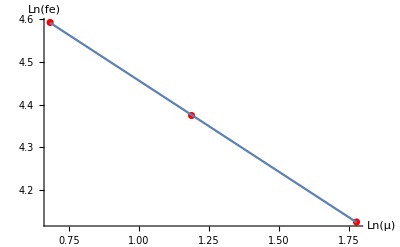

```mathematica
plotlinearfit[{Log[data4[[1]]],Log[data4[[3]]]},linearmodelfitlist[{Log[data4[[1]]],Log[data4[[3]]]}],"Ln(μ)","Ln(fe)"]
```